# Estimating a Population Mean

## Jie Frye Wolfram Summer School 2017

## Learning Objectives

Describe the sampling distribution of sample means.

Draw conclusions about a population mean from a simulation.

Construct a confidence interval to estimate a population mean.

Interpret the confidence interval in context.

Use code to visualize and calculate confidence intervals.

## Overview

#### Inferential statistics

Limited sample of data

Want to know something about the population that this sample comes from.

#### Example

Sample: the body temperature of 100 healthy adults.

Want to know: true population mean body temperature for healthy adults.

#### Certainty

Estimate: The average body temperature is 98.6 .baF.

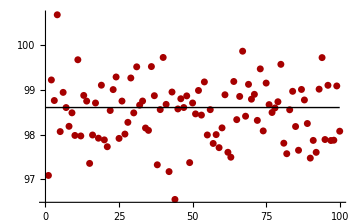

```mathematica
sample=RandomVariate[NormalDistribution[98.6,0.7],100];
ListPlot[sample,Epilog->{Line[{{0,98.6},{100,98.6}}]}]
```

How certain are we?

## Behavior of Sample Means

We use a simulation to collect numerous samples to study the center, spread, and shape of the distribution of sample means. Our goal is to create a probability model that describes the long-run behavior of means from random samples.

Create a variable containing 10000 values with mean 98.6 and standard deviation of 0.7. You have just recorded a population of 10000 individuals body temperatures.

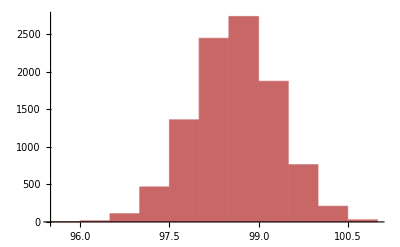

```mathematica
pop=RandomVariate[NormalDistribution[98.6,0.7],10000];
Histogram[pop]
```

Take a random sample of 200 points from this population and calculate the sample mean. Is that a reasonable result?

```mathematica
RandomSample[pop,200];
Mean[%]//N
```

98.5832

Extend your work to create code that will take samples of size n = 200, 400 times, and store the sample means μ in a list.

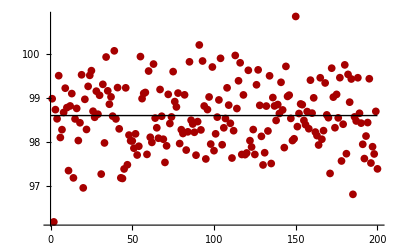
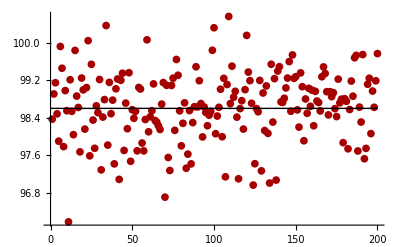
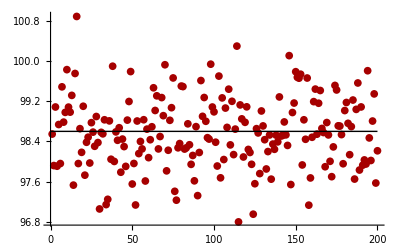
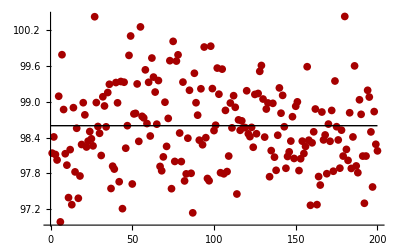
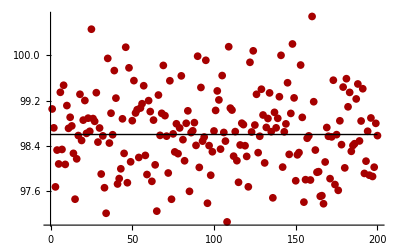
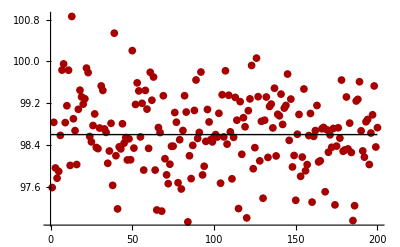
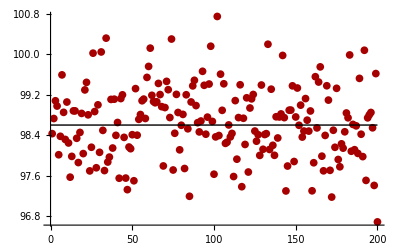
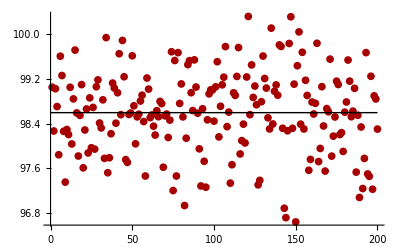

```mathematica
sample=Table[RandomSample[pop,200],{i,400}];
Table[ListPlot[Part[sample,i],Epilog->{Line[{{0,98.6},{200,98.6}}]}],{i,10}]
```

What is the distribution of μ?

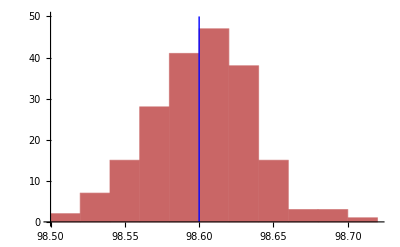

```mathematica
Show[Histogram[Mean[sample]],ContourPlot[{x==98.6},{x,98,99},{y,0,50},ContourStyle->Blue,ColorFunction->Automatic,Frame->False,Axes->True]]
```

## Distribution of Sample Means

Based on what we observed with the simulation, we might expect the following about the distribution of sample means that come from a population where μ = 98.6 and σ = 0.7:

Center: the mean of the distribution of sample means should be μ.

μ_(x̄)=μ

Spread: for large sample size, we expect sample means of body temperatures not to stray too far from the population mean 98.6. Sample means that are very low or very high will be unusual.

σ_(x̄)=σ/(√n)

Shape: the shape of the distribution of sample mean may be somewhat bell-shaped.

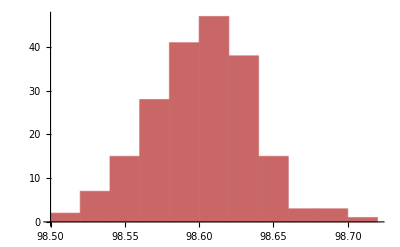
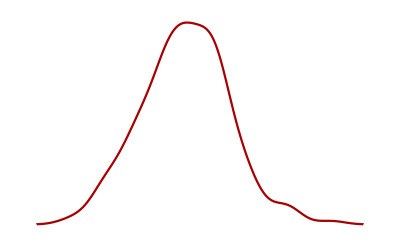

```mathematica
Overlay[{Histogram[Mean[sample]],SmoothHistogram[Mean[sample],Axes->False]}]
```

## Sampling Distribution in Various Populations

From the central limit theorem, the sampling distribution of the sample mean is approximated by N(μ,σ/√n) for infinite populations. In the finite population case, the standard deviation is reduced slightly due to the finite-sample correction factor.

## Confidence Intervals with σ known

When our goal is to estimate μ, we select a random sample from the population and use the x̄ as an estimate.

Since random samples vary, we state the amount of error that may be present.

Because sample means vary in a predictable way, we can make a probability statement about how confident we are in the process we used to estimate μ.

Formula of confidence interval for estimating population mean:

x̄±z·σ/(√n)

The critical value z is associated with desired central areas under the standard normal curve.

```mathematica
f[x_]:=Table[PDF[NormalDistribution[0,σ],x],{σ,{1}}];
g[s_]:=PDF[NormalDistribution[0,1],s];
Manipulate[
Show[ Plot[f[x]//Evaluate,{x,-3,3}],Plot[f[x]//Evaluate,{x,-3,0.00001-InverseCDF[NormalDistribution[0,1],n]},Filling->Axis],Plot[f[x]//Evaluate,{x,3,InverseCDF[NormalDistribution[0,1],n]},Filling->Axis],
Graphics[
{
Line[{{InverseCDF[NormalDistribution[0,1],n],0},{InverseCDF[NormalDistribution[0,1],n],g[InverseCDF[NormalDistribution[0,1],n]]}}],

Line[{{0.0001-InverseCDF[NormalDistribution[0,1],n],0},{0.001-InverseCDF[NormalDistribution[0,1],n],g[InverseCDF[NormalDistribution[0,1],n]]}}],
{Thickness[0.01],Line[{{InverseCDF[NormalDistribution[0,1],n],-0.001},{0.001-InverseCDF[NormalDistribution[0,1],n],0}}]},
Text[Style[Row[{Style["z",Italic]," = ",NumberForm[InverseCDF[NormalDistribution[0,1],n+(1-n)/2],4]}],FontSize->19],{-1.8,0.35}],
Text[Style[Row[{"unshaded area = ",NumberForm[n,2]}],FontSize->14],{-0.35,0.1525}]
}
],
ImageSize->500],
{{n,.90,"confidence level"},.70,.99,Appearance->"Labeled"},SaveDefinitions->True
]
```

## Example (σ known)

Is smoking during pregnancy associated with premature births? To investigate this question, researchers selected a random sample of 114 pregnant women who were smokers. The average pregnancy length for this sample of smokers was 260 days. From a large body of research, it is known that length of human pregnancy has a standard deviation of 16 days.

Based on this study, find a 95% confidence interval for μ, the mean pregnancy length of women who smoke during their pregnancy, and interpret your interval in context.

```mathematica
<<HypothesisTesting`
n=114; mean=260; stddev=16; CL=.95;
NormalCI[mean,stddev,ConfidenceLevel->CL]
```

{228.641,291.359}

Impact of confidence level

```mathematica
Manipulate[
Show[NumberLinePlot[Interval[NormalCI[mean,stddev,ConfidenceLevel->CL]],PlotRange->{220,300}],Graphics[{PointSize[Large],Blue,Point[{mean,1}]}]],
{{CL,.95,"Confidence Level"},.7,.99,Appearance->"Labeled"}]
```

## What Does 95% Confident Really Mean?

“We are 95% confident that the interval from 228.6 and 291.4 actually does contain the true 
value of the population mean μ.”

This means that if we were to select many different samples of size 114 and construct the 
corresponding confidence intervals, 95% of them would contain the true value of the population mean μ.

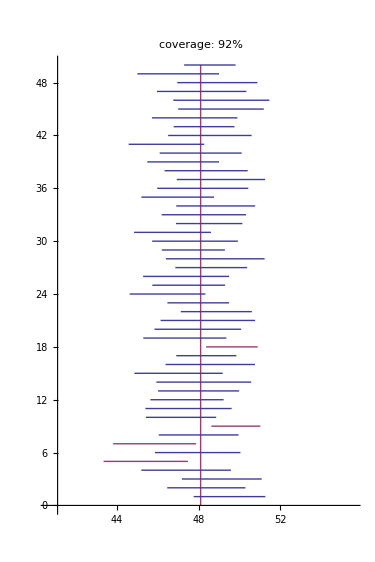

## Rules of Thumb

With σ known, the general rule is that if n is more than 30, the sampling distribution of means will be approximately normal. However, if the population is already normal, then any sample size will produce a normal sampling distribution.

With σ unknown, we will use student t distribution.

## Student T Distribution

The formula for t-score is:

t=(x̄-μ)/(s/√n)

The distribution of t-scores depends on the sample size n. There is a different t-model for every 
n. So the t-model is a family of curves, and we call n − 1 the degrees of freedom or

df=n−1

When is a t-model a good fit for the sampling distribution of sample means?

Use the t-model if the population standard deviation σ is unknown. If σ is known, then use the normal model instead of the t-model.

Use the t-model if variable values are normally distributed in the population. If this is not true, then make sure the sample size is more than 30.

## Confidence Intervals with σ unknown

If the t-model is a good fit for the sampling distribution, then the confidence interval for estimating population mean μ:

x̄±t·s/(√n)

The critical value t is associated with desired central areas under the t distribution.

## Example (σ unknown)

According to the website www.collegedrinkingprevention.gov, “About twenty-five percent of college students report academic consequences of their drinking including missing class, falling behind, doing poorly on exams or papers, and receiving lower grades overall.”

A statistics student is curious about drinking habits of students at his college. He wants to estimate the mean number of alcoholic drinks consumed each week by students at his college. He plans to use a 90% confidence interval. He surveys a random sample of 71 students. The sample mean is 3.93 alcoholic drinks per week. The sample standard deviation is 3.78 drinks.

```mathematica
<<HypothesisTesting`
n=71; mean=3.93; stddev=3.78/Sqrt[n]; CL=.9;
StudentTCI[mean,stddev,n-1,ConfidenceLevel->CL]
```

{3.18222,4.67778}

```mathematica
Manipulate[
Show[NumberLinePlot[Interval[StudentTCI[mean,stddev,n-1,ConfidenceLevel->CL]],PlotRange->{2.5,5.5}],Graphics[{PointSize[Large],Blue,Point[{mean,1}]}]],
{{CL,.9,"Confidence Level"},.7,.99,Appearance->"Labeled"}]
```

## References

E. Hou and E. Madhekar, “Critical Value z* for z-Scores for Confidence Levels”. http://demonstrations.wolfram.com/CriticalValueZForZScoresForConfidenceLevels/

I. McLeod, “Sampling Distribution of the Mean and Standard Deviation in Various Populations”. http://demonstrations.wolfram.com/SamplingDistributionOfTheMeanAndStandardDeviationInVariousPo/